# Physics of Electron Microscopy Instrumentation

## Georgios Varnavides | March 3rd 2026

## Axial Fields & Laplace Equation

## Maxwell & Laplace Symmetries

In the previous lecture, we postulated how electromagnetic focusing depends solely on axial electrostatic and magnetic fields and their gradients.

It might not be immediately obvious why that is the case, so here we briefly expand on the derivation.

### Cylindrical Symmetry Laplace

In the source-free region of a round electrostatic (or magnetic) lens:

	

Therefore

	

With cylindrical symmetry ():

	
	
Which suggests the potential is harmonic and therefore analytic near the optic axis.

```mathematica
Laplacian[ϕ[r,z],{r,θ,z},"Cylindrical"]
```

ϕ^(0,2)[r,z]+(ϕ^(1,0)[r,z])/r+ϕ^(2,0)[r,z]

```mathematica
D[r D[ϕ[r,z],r],r]/r + D[ϕ[r,z],{z,2}]//Simplify
```

ϕ^(0,2)[r,z]+(ϕ^(1,0)[r,z])/r+ϕ^(2,0)[r,z]

### Analytical Expansion

Expanding in powers of :

```mathematica
Series[ϕ[r,z],{r,0,6}]
```

ϕ[0,z]+ϕ^(1,0)[0,z] r+1/2 ϕ^(2,0)[0,z] r^2+1/6 ϕ^(3,0)[0,z] r^3+1/24 ϕ^(4,0)[0,z] r^4+1/120 ϕ^(5,0)[0,z] r^5+1/720 ϕ^(6,0)[0,z] r^6+O[r]^7

and noting that due to cylindrical symmetry, the field is invariant under , the odd terms drop

```mathematica
evenExpansion = Normal[Series[(ϕ[r,z] +ϕ[-r,z])/2,{r,0,6}]]
```

ϕ[0,z]+1/2 r^2 ϕ^(2,0)[0,z]+1/24 r^4 ϕ^(4,0)[0,z]+1/720 r^6 ϕ^(6,0)[0,z]

Plugging this into Laplace’s equation, we can can relate radial derivatives to purely axial derivatives.

```mathematica
evenLaplacian=Simplify[Laplacian[evenExpansion,{r,θ,z},"Cylindrical"]]
```

ϕ^(0,2)[0,z]+2 ϕ^(2,0)[0,z]+1/720 r^2 (360 ϕ^(2,2)[0,z]+480 ϕ^(4,0)[0,z]+r^2 (30 ϕ^(4,2)[0,z]+36 ϕ^(6,0)[0,z]+r^2 ϕ^(6,2)[0,z]))

To do this, we proceed recursively: matching the 1st order coefficients first, and substituting into higher-order ones.

```mathematica
order0Substitutions=Solve[
Coefficient[evenLaplacian,r,0]==0,
Derivative[2,0][ϕ][0,z]
]//First

order2Substitutions=Solve[
Coefficient[evenLaplacian,r,2]==0,
Derivative[4,0][ϕ][0,z]
]//First;

order2Substitutions = order2Substitutions/. D[order0Substitutions,{z,2}]

order4Substitutions=Solve[
Coefficient[evenLaplacian,r,4]==0,
Derivative[6,0][ϕ][0,z]
]//First;

order4Substitutions = order4Substitutions/. D[order2Substitutions,{z,2}]
```

{ϕ^(2,0)[0,z]→-1/2 ϕ^(0,2)[0,z]}

{ϕ^(4,0)[0,z]→3/8 ϕ^(0,4)[0,z]}

{ϕ^(6,0)[0,z]→-5/16 ϕ^(0,6)[0,z]}

Substituting these rules in our even expansion, we obtain the cylindrically-symmetric Laplace equation -- relying only on axial fields and its derivatives.

```mathematica
harmonicExpansion=evenExpansion/.Join[order0Substitutions,order2Substitutions,order4Substitutions]
```

ϕ[0,z]-1/4 r^2 ϕ^(0,2)[0,z]+1/64 r^4 ϕ^(0,4)[0,z]-(r^6 ϕ^(0,6)[0,z])/2304

## Finite Element Fields

Let’s validate this numerically, by comparing the electrostatic potential of an Einzel lens using finite elements!
We’ll use the following axisymmetric geometry:

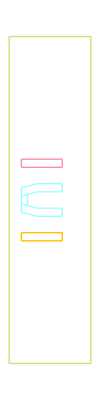

```mathematica
Needs["NDSolve`FEM`"]

geometry=<|"D"->3,"T"->2,"H"->10,"L"->20,"W"->6,"d"->4,"h"->4|>;

electrodeCoords["domain"]=With[{g=geometry},
{
{-2*g["L"],0},
{2*g["L"],0},
{2*g["L"],2*g["H"]},
{-2*g["L"],2*g["H"]}
}/10^3
];

electrodeCoords["left"]=With[{g=geometry},
{
{-g["L"]/2,g["D"]},
{-g["L"]/2 + g["T"],g["D"]},
{-g["L"]/2 + g["T"],g["D"]+g["H"]},
{-g["L"]/2 ,g["D"]+g["H"]}
}/10^3
];

electrodeCoords["middle-left"]=With[{g=geometry},
{
{-g["W"]/2,g["D"]},
{-g["W"]/2+g["T"],g["D"]},
{-g["L"]/2+g["T"]+g["d"]+g["T"],g["D"]+g["h"]},
{-g["L"]/2+g["T"]+g["d"]+g["T"],g["D"]+g["H"]},
{-g["L"]/2+g["T"]+g["d"],g["D"]+g["H"]},
{-g["L"]/2+g["T"]+g["d"],g["D"]+g["h"]}
}/10^3
];

electrodeCoords["middle"]=With[{g=geometry},
{
{-g["W"]/2+g["T"],g["D"]},
{g["W"]/2-g["T"],g["D"]},
{11/8,g["D"]+3/2},
{-11/8,g["D"]+3/2}
}/10^3
];

electrodeCoords["middle-right"]=With[{g=geometry},
{
{g["W"]/2-g["T"],g["D"]},
{g["W"]/2,g["D"]},
{g["L"]/2-g["T"]-g["d"],g["D"]+g["h"]},
{g["L"]/2-g["T"]-g["d"],g["D"]+g["H"]},
{g["L"]/2-g["T"]-g["d"]-g["T"],g["D"]+g["H"]},
{g["L"]/2-g["T"]-g["d"]-g["T"],g["D"]+g["h"]}
}/10^3
];

electrodeCoords["right"]=With[{g=geometry},
{
{g["L"]/2-g["T"],g["D"]},
{g["L"]/2 ,g["D"]},
{g["L"]/2 ,g["D"]+g["H"]},
{g["L"]/2 -g["T"],g["D"]+g["H"]}
}/10^3
];

electrodeCoords["all"]={
electrodeCoords["domain"],
electrodeCoords["left"],
electrodeCoords["middle-left"],
electrodeCoords["middle"],
electrodeCoords["middle-right"],
electrodeCoords["right"]
};

positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
electrodeCoords["flat"]= Join@@electrodeCoords["all"];
electrodeCoords["flat"]=Map[Reverse,electrodeCoords["flat"]];
duplicatePositions=positionDuplicates[electrodeCoords["flat"]];
electrodeCoords["flat"]=DeleteDuplicates[electrodeCoords["flat"]];

Clear[makeSequentialLineElements]
makeSequentialLineElements[l_,offset_:0]:=LineElement[Partition[Append[Range[l],1]+offset,2,1]]

removeDuplicatesAndRenumber[elements_,duplicates_]:=Module[{allIndices,mergeMap,uniqueIndices,reindexMap,finalRules},mergeMap=Flatten[Thread[Rest[#]->First[#]]&/@duplicates];
allIndices=Range[Max[Flatten[elements/. LineElement->Identity]]];
uniqueIndices=Delete[allIndices,List/@Keys[mergeMap]];
reindexMap=Thread[uniqueIndices->Range[Length[uniqueIndices]]];
finalRules=Dispatch[
Join[
mergeMap/. reindexMap,
reindexMap
]
];
elements/. finalRules
]

lengths=Length/@electrodeCoords["all"];
offsets=Accumulate[Prepend[lengths,0]]//Most;

boundaryElements=MapThread[makeSequentialLineElements,{lengths,offsets}];
boundaryElements=removeDuplicatesAndRenumber[boundaryElements,duplicatePositions];
boundaryElements=MapThread[Append,{boundaryElements,Range[Length[boundaryElements]]}];
bmesh=ToBoundaryMesh[
"Coordinates"->electrodeCoords["flat"],
"BoundaryElements"->boundaryElements
];

refinementFunction[vertices_,area_]:=Module[
{centroid,r,z,distToAxis,distToBottom,targetArea},
centroid=Mean[vertices];
r=centroid[[1]];
z=centroid[[2]];
distToAxis=Abs[r];targetArea=Which[
distToAxis<0.002,0.5*10^-8,True,5.0*10^-6 ];
area>targetArea
]

emesh=ToElementMesh[
bmesh,
MeshRefinementFunction->refinementFunction,
MaxCellMeasure->{"Area"->5*10^-6},
"MeshOrder"->2
];

limeColor=RGBColor[211/255,225/255,115/255];
cyanColor=RGBColor[155/255,1,1];
amberColor=RGBColor[1,191/255,0];
pinkColor=RGBColor[1,47/85,161/255];

graphics=bmesh[
"Wireframe"[
"MeshElementStyle"->(Directive[AbsoluteThickness[1],#]&/@{limeColor,amberColor,cyanColor,cyanColor,cyanColor,pinkColor})
]
]
```

We set-up the Laplace equation, using Dirichlet boundary conditions, fixing the potential value at the electrode boundaries:

```mathematica
voltages=<|
"left"->0,"middle-left"->500,"middle"->500,"middle-right"->500,"right"->0
|>;
bcs=MapThread[
DirichletCondition[
phi[r,z]==#1,ElementMarker==#2]&,{Values[voltages],{2,3,4,5,6}}
];

op=Inactive[Div][{{-r,0},{0,-r}}.Inactive[Grad][phi[r,z],{r,z}],{r,z}];
phiSol=NDSolveValue[{op==0,bcs},phi,{r,z}∈ emesh];
```

We can plot the numerical solution on the optical axis

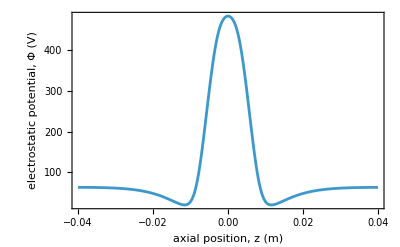

```mathematica
axialField=Plot[Evaluate[phiSol[0,z]],{z,-0.04,0.04},PlotRange->All,Frame->True,FrameLabel->{"axial position, z (m)","electrostatic potential, Φ (V)"}]
```

We expand the numerical solution using only this axial field and plot the two fields near the optic-axis:

```mathematica
harmonicField[r_,z_]=Block[{
phi=phiSol,
phi2=Derivative[0,2][phiSol],
phi4=Derivative[0,4][phiSol]
},
phi[0,z]-r^2/4 phi2[0,z] + r^4/64 phi4[0,z]
];
```

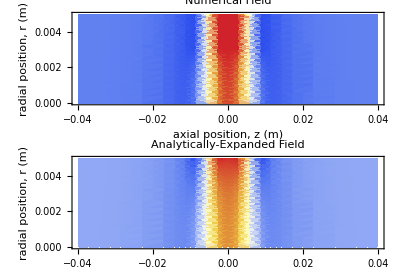

```mathematica
fields=GraphicsColumn[
{
DensityPlot[phiSol[r,z],{z,-0.04,0.04},{r,0,0.005},AspectRatio->1/4,PlotRange->All,ColorFunction->"TemperatureMap",FrameLabel->{"axial position, z (m)","radial position, r (m)"},ImageSize->600,PlotLabel->"Numerical Field"],
DensityPlot[harmonicField[r,z],{z,-0.04,0.04},{r,0,0.005},AspectRatio->1/4,PlotRange->All,ColorFunction->"TemperatureMap",FrameLabel->{"axial position, z (m)","radial position, r (m)"},ImageSize->600,PlotLabel->"Analytically-Expanded Field"]
}
]
```